# 3. izpit – Mathematica

## Computer laboratory 2024/25

Field of Study: Applied Physics and Applied Mathematics

## Student data

Insert your data

Name:

Surname:

Registration Number:

## Instructions

This part of the exam contains two tasks, which together are worth 32 points out of the 100 possible points on the exam.
Solve each task in its own section.

## 1. task [10 points]

1. (5 points) Calculate the limit lim_(z→1+i) (z^4.-1)/(z^2-1)
2. (5 points) Find all such integers m and n, such that it will hold 42 m+2025 n==3. 
The search for solutions in integers can be determined using an additional parameter. Integers.

```mathematica
Limit[(z^4-1)/(z^2-1),z->1+I]
Integrate[x^2Sin[x],{x,0,Pi}]
Solve[42*m+2019*n==3,{m,n},Integers]
```

1+2 ⅈ

-4+π^2

{{m→ConditionalExpression[625+673 C[1], C[1]∈ℤ],n→ConditionalExpression[-13-14 C[1], C[1]∈ℤ]}}

## 2. task [22 points]

1. (6 points) Define the functions f(x)=x^2-x and g(x)=(4-x)/(x^2-6x+9).
2. (6 points) Calculate the value x, where the function f reaches a minimum.
3. (6 points) Draw the graphs of the functions on one image over the interval  [-2,2].
4. (6 points) Numerically calculate the values x, where the graphs of functions f in g on the interval [-2,2] intersect.
Calculate the y-coordinates of the intersections.

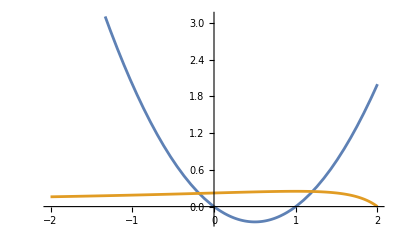

{{x→-0.182271},{x→1.2048}}

{{x→1/2}}

```mathematica
f[x_]:=x^2-x
g[x_]:=(2-x)/(x^2-6x+9)
Plot[{f[x],g[x]},{x,-2,2}]
NSolve[f[x]==g[x],x,Reals]
Solve[f'[x]==0]
```